# Piecewise Fracture Envelope and Yield Surface (paper Figures 2 and 3)

Debug version: every step is its own cell with NO trailing semicolon, so evaluating cell-by-cell (Shift+Enter down the notebook) shows every intermediate value. If something is wrong, the first cell that prints an unexpected value (or an error) tells us exactly where. Once this works, we can put it back together into fewer cells.

Evaluate from the top, one cell at a time, and check each Out[] looks sane before moving to the next.

## Step 1: base parameters (Pa), from base_config.json

```mathematica
q0Pa = 7.75*10^4
```

77500.

```mathematica
tensileTPa = 7.0*10^4
```

70000.

```mathematica
fractureAngleDeg = 10
```

10

```mathematica
dpPhiDeg = 58
```

58

```mathematica
dpThresholdPPa = -300
```

-300

```mathematica
yieldFrictionAngleDeg = 6
```

6

```mathematica
cfFresh = 0.95
```

0.95

```mathematica
cfMid1 = 0.7
```

0.7

```mathematica
cfMid2 = 0.4
```

0.4

```mathematica
cfResidual = 0.1
```

0.1

```mathematica
compressiveThresholdPa = q0Pa/0.4*1.1
```

213125.

## Step 2: convert to kPa

```mathematica
q0 = q0Pa/1000.
```

77.5

```mathematica
tensileT = tensileTPa/1000.
```

70.

```mathematica
dpThresholdP = dpThresholdPPa/1000.
```

-0.3

```mathematica
compressiveThreshold = compressiveThresholdPa/1000.
```

213.125

## Step 3: derived slopes (tangents of the angles)

```mathematica
fractureAngleTan = Tan[fractureAngleDeg Degree]
```

Tan[10 °]

```mathematica
dpTanPhi = Tan[dpPhiDeg Degree]
```

Cot[32 °]

```mathematica
yieldFrictionTan = Tan[yieldFrictionAngleDeg Degree]
```

Tan[6 °]

## Step 4: crossover point (where the steep DP leg would meet the intact envelope)

```mathematica
pIntersect = (q0 + dpTanPhi*dpThresholdP)/(dpTanPhi - fractureAngleTan)
```

54.0867

```mathematica
qIntersect = q0 + fractureAngleTan*pIntersect
```

87.0369

Sanity check: qIntersect should equal qIntact[pIntersect] exactly (the crossover, by construction, sits on the intact envelope's compression-shear leg). Both lines below should print the same number.

```mathematica
qIntersect
```

87.0369

```mathematica
q0 + fractureAngleTan*pIntersect
```

87.0369

## Step 5: Cf-scaled crossover (fresh crack vs. worked rubble)

```mathematica
qCrossoverFresh = qIntersect*cfFresh
```

82.6851

```mathematica
qCrossoverResidual = qIntersect*cfResidual
```

8.70369

```mathematica
pCrossoverFresh = dpThresholdP + qCrossoverFresh/dpTanPhi
```

51.3674

```mathematica
pCrossoverResidual = dpThresholdP + qCrossoverResidual/dpTanPhi
```

5.13867

## Step 6: define qIntact[p] and test it at three points

```mathematica
qIntact[p_] := If[p <= 0, (q0/tensileT)*(p + tensileT), q0 + fractureAngleTan*p]
```

Expected: 0 at p = -tensileT, q0 at p = 0, and something above q0 at the compressive threshold.

```mathematica
qIntact[-tensileT]
```

0.

```mathematica
qIntact[0]
```

77.5

```mathematica
qIntact[compressiveThreshold]
```

115.08

## Step 7: define qYield[p, cf] and test it at a few points

```mathematica
qYield[p_, cf_] := Which[
   p < dpThresholdP, 0,
   True, Min[(p - dpThresholdP)*dpTanPhi,
             qIntersect*cf + yieldFrictionTan*(p - dpThresholdP - (qIntersect*cf)/dpTanPhi)]
]
```

Expected: 0 below dpThresholdP, small near p = 0, and qCrossoverFresh / qCrossoverResidual (computed in Step 5) right at pCrossoverFresh / pCrossoverResidual.

```mathematica
qYield[dpThresholdP - 1, cfFresh]
```

0

```mathematica
qYield[0, cfFresh]
```

0.4801

```mathematica
qYield[pCrossoverFresh, cfFresh]
```

82.6851

```mathematica
qYield[pCrossoverResidual, cfResidual]
```

8.70369

```mathematica
qYield[compressiveThreshold, cfFresh]
```

99.6865

```mathematica
qYield[compressiveThreshold, cfResidual]
```

30.5639

## Step 8: plot ranges

```mathematica
textSize = 24
```

24

```mathematica
textSize2 = 24
```

24

```mathematica
hPad = 20
```

20

```mathematica
pMin = -tensileT - hPad
```

-90.

```mathematica
pMax = compressiveThreshold + hPad
```

233.125

```mathematica
qTopEnvelope = qIntact[compressiveThreshold]
```

115.08

```mathematica
qTopYieldFresh = qYield[compressiveThreshold, cfFresh]
```

99.6865

```mathematica
qTopYieldResidual = qYield[compressiveThreshold, cfResidual]
```

30.5639

```mathematica
qPlotMax = 1.2*Max[qTopEnvelope, qTopYieldFresh, qTopYieldResidual]
```

138.096

## Step 10: Figure 2 -- fracture envelope, styled

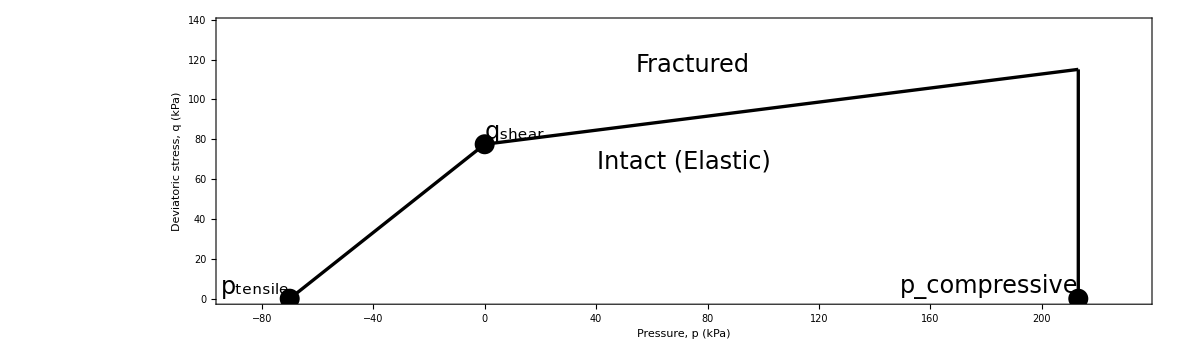

```mathematica
p1 = Plot[qIntact[p], {p, pMin, compressiveThreshold},
  PlotRange -> {{pMin, pMax}, {0, qPlotMax}},
  PlotStyle -> {Thickness[0.002], Black},
  Frame -> True,
  FrameLabel -> {"Pressure, p (kPa)", "Deviatoric stress, q (kPa)"},
  FrameStyle -> Directive[Black, Thickness[0.002]],
  BaseStyle -> {FontSize -> textSize, FontFamily -> "Times New Roman"},
  AspectRatio -> 0.3,
  ImageSize -> 1200,
  Epilog -> {
    PointSize[0.012], Black,
    Point[{-tensileT, 0}],
    Point[{0, q0}],
    Point[{compressiveThreshold, 0}],
    Text[Style["\!\(\*SubscriptBox[\(p\), \(tensile\)]\)", textSize2],
      {-tensileT, 0}, {+0.9, -1.75}],
    Text[Style["\!\(\*SubscriptBox[\(q\), \(shear\)]\)", textSize2],
      {0, q0}, {-0.5, -1.9}],
    Text[Style["\!\(\*SubscriptBox[\(p\), \(compressive\)]\)", textSize2],
      {compressiveThreshold, 0}, {1.2, -1.75}],
    Text[Style["Intact (Elastic)", Black, textSize2],
      {(pMin + pMax)/2, qPlotMax/2}],
    Text[Style["Fractured", Black, textSize2],
      {compressiveThreshold*0.35, qPlotMax*0.85}],
    Thickness[0.002], Black,
    Line[{{compressiveThreshold, qTopEnvelope}, {compressiveThreshold, 0}}]
  }]
```

## Step 11: Figure 3 -- yield surface, four Cf states, styled

All four curves share the same steep Drucker-Prager segment near p_threshold (independent of Cf) -- Cf only sets how far that segment extends before kinking onto the shallower second leg. High Cf (fresh crack) kinks late, so the material sustains more shear before yielding; low Cf (worked/residual rubble) kinks almost immediately, so it yields at much lower shear. q_yield marks the fresh curve's kink point as a reference; p_compressive is where all curves are cut off (the pressure cap).

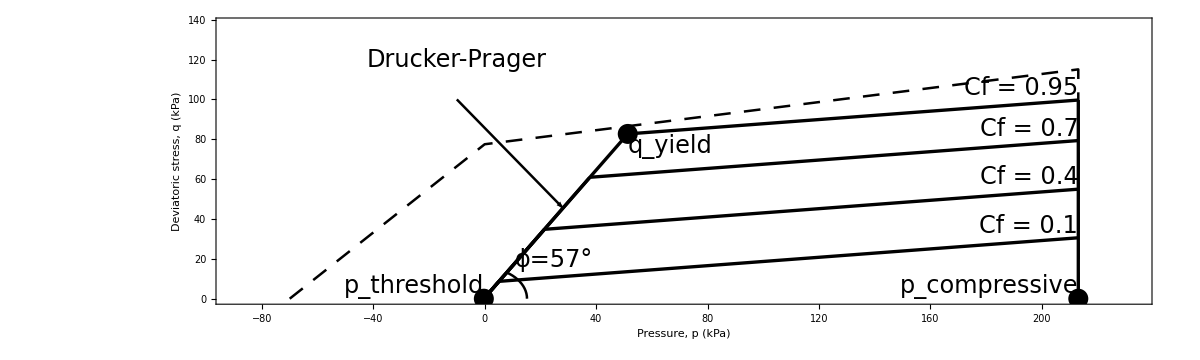

```mathematica
p2 = Plot[{qYield[p, cfFresh], qYield[p, cfMid1], qYield[p, cfMid2], qYield[p, cfResidual]},
  {p, dpThresholdP, compressiveThreshold},
  PlotRange -> {{pMin, pMax}, {0, qPlotMax}},
  PlotStyle -> {{Thickness[0.002], Black},
    {Thickness[0.002], Black},
    {Thickness[0.002], Black},
    {Thickness[0.002], Black}},
  Frame -> True,
  FrameLabel -> {"Pressure, p (kPa)", "Deviatoric stress, q (kPa)"},
  FrameStyle -> Directive[Black, Thickness[0.002]],
  BaseStyle -> {FontSize -> textSize, FontFamily -> "Times New Roman"},
  AspectRatio -> 0.3,
  ImageSize -> 1200,
  Epilog -> {
    Thickness[0.002], Black,
    Line[{{compressiveThreshold, Max[qTopYieldFresh, qTopYieldResidual]},
      {compressiveThreshold, 0}}],
    Thickness[0.0015], Black, Dashing[{0.01, 0.008}],
    Line[{{-tensileT, 0}, {0, q0}, {compressiveThreshold, qTopEnvelope}, {compressiveThreshold, 0}}],
    PointSize[0.012], Black,
    Point[{dpThresholdP, 0}],
    Point[{compressiveThreshold, 0}],
    Point[{pCrossoverFresh, qCrossoverFresh}],
    Text[Style["\!\(\*SubscriptBox[\(p\), \(threshold\)]\)", textSize2],
      {dpThresholdP, 0}, {1.4, -1.75}],
    Text[Style["\!\(\*SubscriptBox[\(p\), \(compressive\)]\)", textSize2],
      {compressiveThreshold, 0}, {1.2, -1.3}],
    Text[Style["\!\(\*SubscriptBox[\(q\), \(yield\)]\)", textSize2],
      {pCrossoverFresh, qCrossoverFresh}, {-1.3, +0.8}],
    Text[Style["Cf = " <> ToString[cfFresh], textSize2],
      {compressiveThreshold, qYield[compressiveThreshold, cfFresh]}, {1.3, -0.8}],
    Text[Style["Cf = " <> ToString[cfMid1], textSize2],
      {compressiveThreshold, qYield[compressiveThreshold, cfMid1]}, {1.3, -0.9}],
    Text[Style["Cf = " <> ToString[cfMid2], textSize2],
      {compressiveThreshold, qYield[compressiveThreshold, cfMid2]}, {1.3, -1.0}],
    Text[Style["Cf = " <> ToString[cfResidual], textSize2],
      {compressiveThreshold, qYield[compressiveThreshold, cfResidual]}, {1.3, -1.0}],
    Thickness[0.0015], Black, Dashing[None],
    Circle[{dpThresholdP, 0}, 0.3*(pCrossoverFresh - dpThresholdP), {0, dpPhiDeg Degree}],
    Text[Style["ϕ=57°", textSize2],
      {dpThresholdP + 0.42*(pCrossoverFresh - dpThresholdP)*Cos[dpPhiDeg Degree/2]+6,
       0.42*(pCrossoverFresh - dpThresholdP)*Sin[dpPhiDeg Degree/2]+9}],
    {Thickness[0.0015], Black, Dashing[None], Arrowheads[0.015],
     Arrow[{{-10, 100}, {dpThresholdP + 0.55*(pCrossoverFresh - dpThresholdP), 0.55*qCrossoverFresh}}]},
    Text[Style["Drucker-Prager", textSize2], {-10, 120}, {0, 1.2}]
  }]
```

## Step 13: export

Run these only after p1, p2, p3 above all look right. Each Export returns the path it wrote, so you'll see confirmation output.

```mathematica
figuresDir = FileNameJoin[{NotebookDirectory[], "..", "..", "_paper", "figures"}]
```

/home/s2/Projects-CUDA/iceMPM_v5/_python_code/mathematica/../../_paper/figures

```mathematica
Export[FileNameJoin[{figuresDir, "fracture_envelope_new.svg"}], p1]
```

/home/s2/Projects-CUDA/iceMPM_v5/_python_code/mathematica/../../_paper/figures/fracture_envelope_new.svg

```mathematica
Export[FileNameJoin[{figuresDir, "yield_surface_new.svg"}], p2]
```

/home/s2/Projects-CUDA/iceMPM_v5/_python_code/mathematica/../../_paper/figures/yield_surface_new.svg